## QMC

This document is an attempt to write a Metropolis Monte Carlo for Quantum Spin problems. At least here we would focus on visualization aspects since a lot of it has to do with the physics.

First we need to define the system. Our first attempt is a 2D square lattice on spins which can be defined as a Matrix. 
(We choose array since it makes life easier to switch between dimensions and lattice size.

Linear Lattice Dimension = m

```mathematica
m=6;
A=ConstantArray[1,{m,m}]
```

{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}

(1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1)

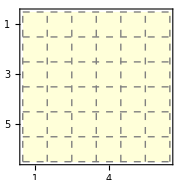

```mathematica
A//MatrixForm
MatrixPlot[A,ColorRules->{-1->LightBlue,1->LightYellow},Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Small]
```

This was one of the ground-state configurations. We can randomize it as follows.

(1 | -1 | -1 | -1 | -1 | -1
1 | -1 | -1 | 1 | -1 | 1
-1 | 1 | -1 | 1 | -1 | 1
-1 | 1 | -1 | 1 | -1 | 1
-1 | -1 | -1 | -1 | -1 | 1
1 | -1 | 1 | 1 | -1 | 1)

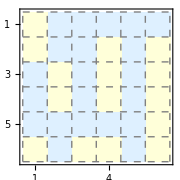

```mathematica
For[i=1,i<(m+1),i++,
For[j=1,j<(m+1),j++,
A[[i,j]]=2*RandomInteger[{0,1}]-1;
]
]

A//MatrixForm
MatrixPlot[A,ColorRules->{-1->LightBlue,1->LightYellow},Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Small]
```

One Key aspect of the Monte Carlo is randomly inverting a spin to generate a new configuration. This can be achieved as follows.
First choose the location randomly. And then invert the spin.

(1 | -1 | -1 | -1 | -1 | -1
1 | -1 | -1 | -1 | -1 | 1
-1 | 1 | -1 | 1 | -1 | 1
-1 | 1 | -1 | 1 | -1 | 1
-1 | -1 | -1 | -1 | -1 | 1
1 | -1 | 1 | 1 | -1 | 1)

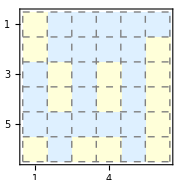

```mathematica
a=RandomInteger[{1,m}];
b=RandomInteger[{1,m}];
A[[a,b]]=-1*A[[a,b]];

A//MatrixForm
MatrixPlot[A,ColorRules->{-1->LightBlue,1->LightYellow},Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Small]
```

Now we introduce the functional, Energy.
We first treat the Ising Model (without magnetic field).

Future Plans: Ising Model, Bose-Hubbard Model, Fermi Hubbard Model with particle hole symmetry.
Interaction Strength: J

At some point we will define a magnetic field as an array, we reserve h for the same.

```mathematica
J=1;
Energy=0;


For[i=1,i<(m+1),i++,
Energy= Energy-J*Sum[A[[i,j]]*A[[i,j+1]],{j,1,(m-1)}];
];
For[j=1,j<(m+1),j++,
Energy=Energy-J*Sum[A[[i,j]]*A[[i+1,j]],{i,1,(m-1)}];
];

For[i=1,i<(m+1),i++,
Energy= Energy-J*A[[i,1]]*A[[i,m]];
];
For[j=1,j<(m+1),j++,
Energy=Energy-J*A[[1,j]]*A[[m,j]];
];


Energy
```

-4

## Appendices

#### Exporting Animations as gif

```mathematica
https://www.youtube.com/watch?v=CMor1VtBZzA
```

Break Manipulate into function, and manipulate, then import as a table.